```mathematica
onestep[f_,g_,α_,{ϕ1_,ϕ2_},umax_]:=Module[{samples,us=Table[(umax i)/200,{i,1,200}]},samples=Table[{{u+ⅈ u},NIntegrate[f[ϕ1[u Exp[-α y]]+ⅈ ϕ2[u Exp[-α y]]] g[y],{y,0,∞}]},{u,us}];{Interpolation[Prepend[Re[samples],{{0},1,0}],Method->"Hermite"],Interpolation[Prepend[Im[samples],{{0},0,1}],Method->"Hermite"]}]
```

```mathematica
alphahelper[g_,a_?NumericQ]:=NIntegrate[g[t] Exp[-a t],{t,0,∞}]
findalpha[f_,g_]:=α/.FindRoot[f'[1] alphahelper[g,α]-1,{α,1,0,∞}]
```

```mathematica
forward[f_,g_,umax_]:=Module[{α=findalpha[f,g],initial=1/(1-ⅈ #1)&},Nest[onestep[f,g,α,#1,umax]&,{Re[initial[#]]&,Im[initial[#]]&},10]]
```

```mathematica
ift[ϕ_,umax_]:=Table[{t,Re[NIntegrate[Exp[-ⅈ u t] ϕ[u],{u,0,umax}]]/π},{t,-1,5,0.1}]
```

```mathematica
findalpha[#1^2&,PDF[GammaDistribution[2,1/2],#]&]
```

0.828427

```mathematica
Integrate[1/(1+x^n),{x,0,∞},Assumptions->{n>1}]
1/%==Sinc[π/n]//FullSimplify
Integrate[Sinc[π/n]/(1+x^n), {x,0,∞},Assumptions->{n>1}]
```

(π Csc[π/n])/n

True

1

```mathematica
powerdist[n_]:=(Sinc[π/n] UnitStep[#1-1/2])/(1+(#1-1/2)^n)&
```

(Sinc[π/2] UnitStep[#1-1/2])/(1+(#1-1/2)^2)&

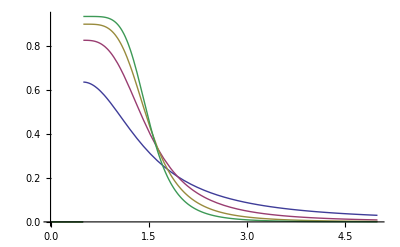

```mathematica
Plot[Table[powerdist[n][x],{n,2,5}]//Evaluate,{x,0,5},PlotRange->All]
```

```mathematica
Table[findalpha[#1^2&,powerdist[n]],{n,2,5}]
```

{0.380625,0.559126,0.626213,0.657832}

```mathematica
powerdist[2]//FullSimplify
```

(Sinc[π/2] UnitStep[#1-1/2])/(1+(#1-1/2)^2)&

```mathematica
PDF[GammaDistribution[2,1/2],t]
```

Piecewise[{{4 ⅇ^(-2 t) t, t>0}, {0, True}}]

```mathematica
1-CDF[GammaDistribution[2,1/2],10]//N
```

4.32842×10^-8

```mathematica
powercdf[n_,t_?NumericQ]:=NIntegrate[powerdist[n][y],{y,0,t}]
```

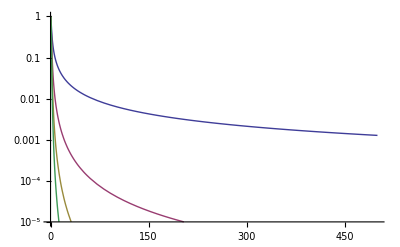

```mathematica
LogPlot[Table[1-powercdf[n,x],{n,2,5}]//Evaluate,{x,0,500},PlotRange->{10^-5,1}]
```

```mathematica
PDF[GammaDistribution[β,1/β],t];
FullSimplify[%,Assumptions->{β>1,t>0}]
```

(ⅇ^(-t β) t^(-1+β) β^β)/Gamma[β]

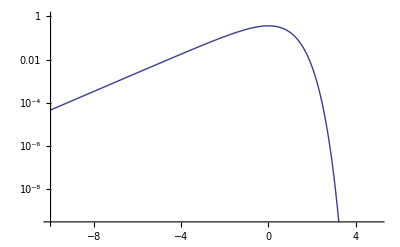

```mathematica
LogPlot[Exp[-Exp[t]] Exp[t], {t,-10,5}]
```

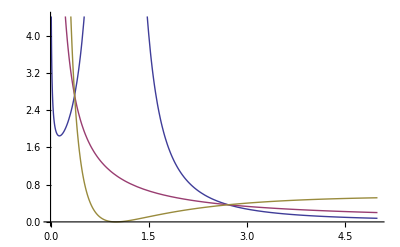

```mathematica
Plot[{1/W 1/Log[W]^2,1/W,1/W*Log[W]^2},{W,0,5}]
```

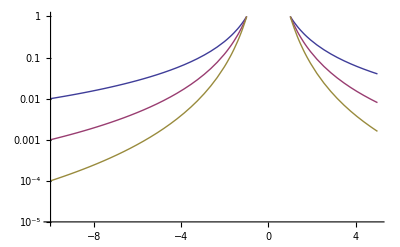

```mathematica
LogPlot[{1/Abs[x]^2,1/Abs[x]^3,1/Abs[x]^4},{x,-10,5},PlotRange->{10^-5,1}]
```

(ⅇ^(-ⅇ^s β) (ⅇ^s)^β β^β)/Gamma[β]

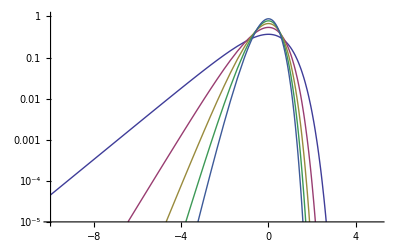

```mathematica
(ⅇ^(-t β) t^(-1+β) β^β)/Gamma[β]*t /.t->Exp[s]
LogPlot[%/.β->{1,2,3,4,5}//Evaluate,{s,-10,5},PlotRange->{10^-5,1}]
```

```mathematica
order[f_]:=Module[{df=D[f[z], z]},Limit[(z df)/f[z],z->0]]
```

{0,1,2,3,4,5,6,7,8}

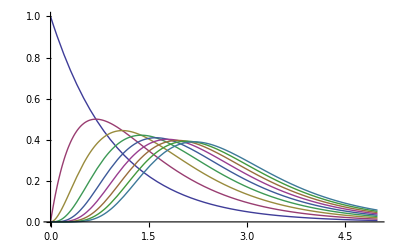

```mathematica
Table[order[Function[t,(k-1) Exp[-(k-1) t] (ⅇ^t-1)^(k-2)]],{k,2,10}]
Plot[Evaluate[ Table[(k-1) Exp[-(k-1) t] (ⅇ^t-1)^(k-2),{k,2,10}]],{t,0,5}]
```

```mathematica
Integrate[t (k-1) Exp[-(k-1) t] (ⅇ^t-1)^(k-2),{t,0,∞},Assumptions->{k≥2,k∈Integers}]
```

EulerGamma+PolyGamma[0,k]

```mathematica
Limit[(EulerGamma+PolyGamma[0,k])/Log[k],k->∞]
```

1

(ⅇ^(t (1-k β)) (-1+ⅇ^t)^(-1+(-1+k) β) Gamma[k β])/(Gamma[β] Gamma[(-1+k) β])

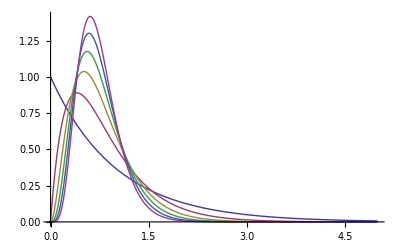

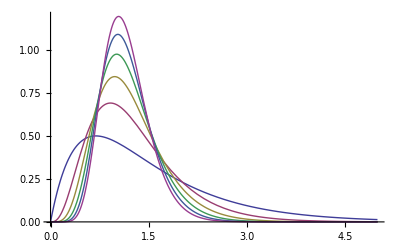

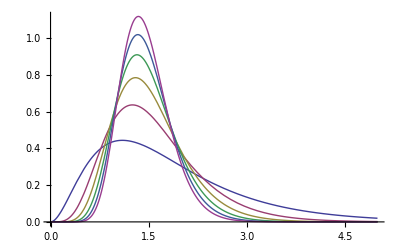

```mathematica
Gamma[k β]/Gamma[β]/Gamma[(k-1)β] Exp[-(k β-1)t](Exp[t]-1)^((k-1)β-1)
Plot[Table[%/.k->2,{β,1,6}]//Evaluate,{t,0,5}]
Plot[Table[%%/.k->3,{β,1,6}]//Evaluate,{t,0,5}]
Plot[Table[%%%/.k->4,{β,1,6}]//Evaluate,{t,0,5}]
Manipulate[Plot[%%%%,{t,0,5},PlotRange->All],{k,2,20,1},{β,1,40}]
```

```mathematica
order[Function[t,Gamma[k β]/Gamma[β]/Gamma[(k-1)β] Exp[-(k β-1)t](Exp[t]-1)^((k-1)β-1)]]
```

-1+(-1+k) β

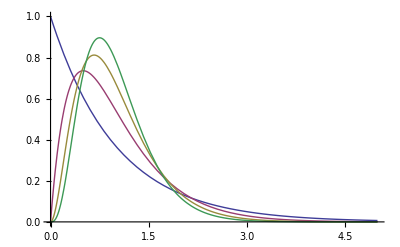

```mathematica
Plot[Table[PDF[GammaDistribution[β,1/β],t],{β,1,4}]//Evaluate,{t,0,5}]
```

```mathematica
Integrate[(ⅇ^(-t β) t^(-1+β) (1/β)^-β)/Gamma[β] Exp[-α t],{t,0,∞}]
```

ConditionalExpression[(1/β)^-β (α+β)^-β,Re[α+β]>0&&Re[β]>0]

```mathematica
Solve[(1/β)^-β (α+β)^-β==1/2,α]
FullSimplify[%,Assumptions->β>1]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{α→-((1/β)^β)^(-1/β) (-2^(1/β)+((1/β)^β)^(1/β) β)}}

{{α→(-1+2^(1/β)) β}}

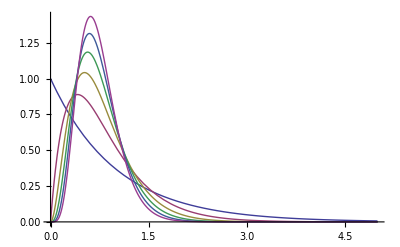

```mathematica
Plot[Table[ PDF[GammaDistribution[β,1/β],t/((-1+2^(1/β)) β)]/((-1+2^(1/β)) β ),{β,1,6}]//Evaluate,{t,0,5}]
```

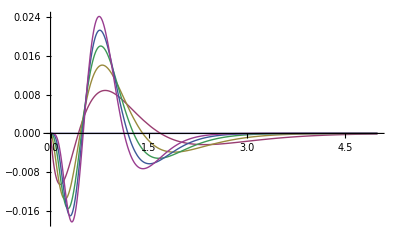

```mathematica
Plot[Table[((-1+2^(1/β))^-β ⅇ^(-t/(-1+2^(1/β))) t^(-1+β))/Gamma[β]-(ⅇ^(t (1-k β)) (-1+ⅇ^t)^(-1+(-1+k) β) Gamma[k β])/(Gamma[β] Gamma[(-1+k) β])/.k->2,{β,1,6}]//Evaluate,{t,0,5},PlotRange->All]
```

```mathematica
Integrate[t (ⅇ^(t (1-k β)) (-1+ⅇ^t)^(-1+(-1+k) β) Gamma[k β])/(Gamma[β] Gamma[(-1+k) β]),{t,0,∞},Assumptions->{k≥2,β≥1}]
```

-1/(k β)-HarmonicNumber[-1+β]+HarmonicNumber[k β]

```mathematica
Integrate[(-1/(k β)-HarmonicNumber[-1+β]+HarmonicNumber[k β])(ⅇ^(t (1-k β)) (-1+ⅇ^t)^(-1+(-1+k) β) Gamma[k β])/(Gamma[β] Gamma[(-1+k) β])/.t->y*(-1/(k β)-HarmonicNumber[-1+β]+HarmonicNumber[k β])//Evaluate,{y,0,∞},Assumptions->{k≥2,β≥1}]
```

$Aborted

```mathematica
(-1/(k β)-HarmonicNumber[-1+β]+HarmonicNumber[k β])(ⅇ^(t (1-k β)) (-1+ⅇ^t)^(-1+(-1+k) β) Gamma[k β])/(Gamma[β] Gamma[(-1+k) β])/.t->y*(-1/(k β)-HarmonicNumber[-1+β]+HarmonicNumber[k β])
FullSimplify[%/.y->t,Assumptions->{k≥2,β≥1}]
```

(ⅇ^(y (1-k β) (-1/(k β)-HarmonicNumber[-1+β]+HarmonicNumber[k β])) (-1+ⅇ^(y (-1/(k β)-HarmonicNumber[-1+β]+HarmonicNumber[k β])))^(-1+(-1+k) β) Gamma[k β] (-1/(k β)-HarmonicNumber[-1+β]+HarmonicNumber[k β]))/(Gamma[β] Gamma[(-1+k) β])

(ⅇ^(t (1-k β) (-1/(k β)-HarmonicNumber[-1+β]+HarmonicNumber[k β])) (-1+ⅇ^(t (-1/(k β)-HarmonicNumber[-1+β]+HarmonicNumber[k β])))^(-1+(-1+k) β) Gamma[k β] (-1/(k β)-HarmonicNumber[-1+β]+HarmonicNumber[k β]))/(Gamma[β] Gamma[(-1+k) β])

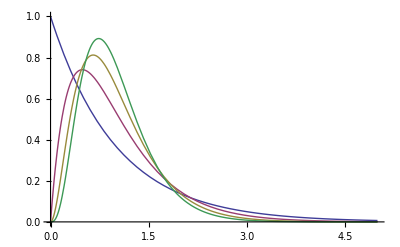

```mathematica
Plot[Table[(ⅇ^(t (1-k β) (-1/(k β)-HarmonicNumber[-1+β]+HarmonicNumber[k β])) (-1+ⅇ^(t (-1/(k β)-HarmonicNumber[-1+β]+HarmonicNumber[k β])))^(-1+(-1+k) β) Gamma[k β] (-1/(k β)-HarmonicNumber[-1+β]+HarmonicNumber[k β]))/(Gamma[β] Gamma[(-1+k) β])/.k->2,{β,1,4}]//Evaluate,{t,0,5}]
```

```mathematica
(ⅇ^(t (1-k β) (-1/(k β)-HarmonicNumber[-1+β]+HarmonicNumber[k β])) (-1+ⅇ^(t (-1/(k β)-HarmonicNumber[-1+β]+HarmonicNumber[k β])))^(-1+(-1+k) β) Gamma[k β] (-1/(k β)-HarmonicNumber[-1+β]+HarmonicNumber[k β]))/(Gamma[β] Gamma[(-1+k) β])/.{k->2,β->4}
```

319/3 ⅇ^(-319 t/60) (-1+ⅇ^(319 t/420))^3

```mathematica
norm[n_]:= (-1+2 n) ExpIntegralE[2 n,2 n]
logdist[n_]:=Function[x,Evaluate[1/(x norm[n])(norm[n] 2^(-1+2 n) n^(-1+2 n) (-1+2 n) Log[x norm[n]]^(-2 n)) UnitStep[Exp[-2 n]-x norm[n]]]]
```

```mathematica
Exp[-2*1]/norm[1]//N
```

3.60565

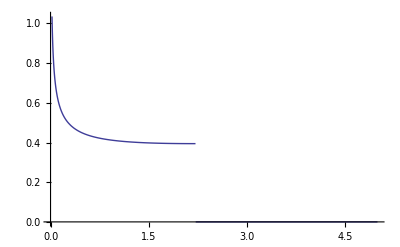

```mathematica
Plot[logdist[4][x],{x,0,5}]
```